Morgan Nance Homework 7
Question 1

```mathematica
(*get equilibrium values from dG*)
dGdeox=-14.3; (*kcal/mol*)
dGox=-8; (*kcal/mol*)
RT=0.59; (*kcal/mol*)
kdeox=Exp[(-dGdeox)/(RT)];
kox=Exp[(-dGox)/(RT)];
```

```mathematica
(*get the x-values by getting a range of total dimer*)
exponents=Range[-15,0,0.1];
totald=Table[10^x,{x,exponents}];
```

```mathematica
(*collect y-values from total dimer by using a fancy equation*)
fractionddeox=(-1+(Sqrt[1+(8*kdeox*totald)]))/(4*kdeox*totald);
fractiondox=(-1+(Sqrt[1+(8*kox*totald)]))/(4*kox*totald);
```

```mathematica
(*put the data together in an {x,y} format*)
ddeoxdata=Transpose[{exponents,fractionddeox}];
doxdata=Transpose[{exponents,fractiondox}];
```

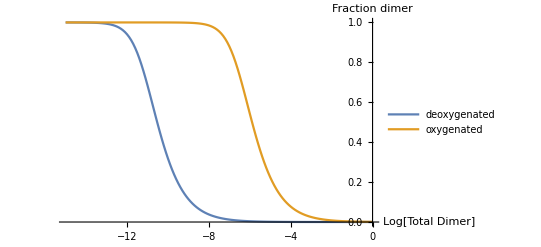

```mathematica
(*plot the data*)
ListLinePlot[{ddeoxdata,doxdata},AxesLabel->{"Log[Total Dimer]","Fraction dimer"},PlotLegends->{"deoxygenated","oxygenated"}]
```

```mathematica
Question 3
```

```mathematica
(*https://www.ncbi.nlm.nih.gov/pubmed/21389271*)
z=9;
RT=0.59; (*kcal/mol*)
pkafolded=6.5;
pkaunfolded=7.5;
```

```mathematica
(*x-values*)
pH=Range[0,14,0.1];
```

```mathematica
dGvalues=-RT*Log[(1+Exp[z*2.3*(pH-pkaunfolded)])/(1+Exp[z*2.3*(pH-pkafolded)])];
```

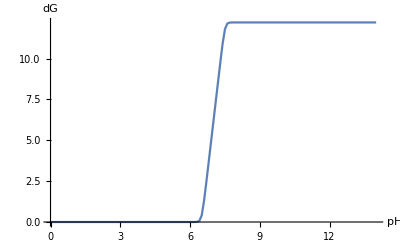

```mathematica
ListLinePlot[Transpose[{pH,dGvalues}],AxesLabel->{"pH","dG"}]
```

```mathematica
Question 9
```

```mathematica
z2=1;
RT=0.59;
pkaU=4.5;
pkaF=9;
pH=Range[0,14,0.1];
(*adding 11.8 because we're assuming that is the basal stability*)
dGvalues2=-RT*Log[(1+Exp[z2*2.3*(pH-pkaU)])/(1+Exp[z2*2.3*(pH-pkaF)])]+11.8;
```

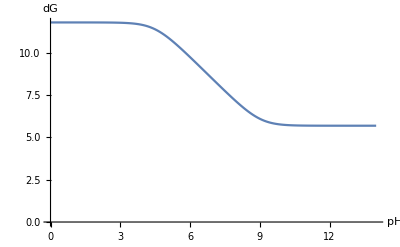

```mathematica
ListLinePlot[Transpose[{pH,dGvalues2}],AxesLabel->{"pH","dG"}]
```